```mathematica
f[xa_,na_,sa_]:=
Module[
{df,dont,e,expr,final,fn,fn1,global,global1,HashTable,intervals,intervals1,intervals2,list,max,max1,min,min1,n,opts,s,sin,SSin,strings,uspec,x3,global2,dal,global3,da,hio,final1,doit,expression,f1,hey,hio1,go,hey1,finala,nice},
expression = ToExpression[xa];
doit = StringJoin["This function plots ",xa,". "];
hey = "";
f1 = "";
hey1="";
If[Exponent[expression,x]≠ 0 ,f1 = StringJoin["This function is polynomial. ","The exponent of this function is ",ToString[Exponent[expression,x]],". "]];
If[FunctionPeriod[expression ,x]≠ 0,
hey1=StringJoin[ "This function is Periodic so probably trigonometric with a period of ",ToString[FunctionPeriod[expression ,x]],". "]];
fn = expression;
da = Plot[fn,{x,na,sa}];
Print[da];
max = x/. N[List[Solve[{na≤x≤sa, D[fn,x]==0,D[fn, {x,2}]≤0},x]]]//Flatten;
 min= x/.  N[List[Solve[{na≤x≤sa, D[fn,x]==0,D[fn, {x,2}]≥ 0},x]]] // Flatten;
nice = StringJoin["This function has  a total of ",ToString[Length[max]+Length[min]]," extremas . "];
max1 = Table[{{max⟦x3⟧,Round[fn/. x-> max⟦x3⟧,0.0001]}},{x3,1,Length[max]}];
max1=  N[Flatten[max1,1]];
min1 =N[Flatten[Table[{{{min⟦x3⟧,Round[fn/.x-> min⟦x3⟧,0.0001]}}},{x3,1,Length[min]}]],1];
{min,max}={NMinValue[{D[fn,x],na≤x≤sa},x],NMaxValue[{D[fn,x],na≤x≤sa},x]};
df=Rescale[D[fn,x],{min,max},{0,1}];
global =x/.N[ List[Solve[{na≤x≤sa, D[fn,x]==0},x]]] // Flatten;
global = Sort[global];
global2 = Insert[global,na,1];
global1 = global2[[2;;Length[global2]]];
global3 = Insert[global1,sa,Length[global1]+1];
intervals = Transpose[{global2,global3}];
dal = "A proposed description of this plot based on the derivatives and extremas : ";
dont = Table[Mean[Table[df/. {x-> x1} , {x1,intervals[[n,1]],intervals[[n,2]],0.01}]],{n,1,Length[intervals]}];
strings = List["a very sharp decrease","a sharp decrease","a smooth decline","still a smooth decline","still a smooth decline/increase or most likely no change at all","a very smooth increase","a very smooth increase","a smooth increase","a sharp increase","a very sharp increase"];
final = Table[{strings[[If[((dont[[x]]≥  0.5)|| (dont[[x]] < 0.1)),(Round[dont[[x]],0.1]*10)+1, (Round[dont[[x]],0.1]*10 )]]]," that ends at x = ",ToString[intervals[[x,2]]]," then "},{x,1,Length[dont]}];
final1 = final// Flatten;
doit = StringJoin[doit,hey,f1,hey1,nice,dal,final1];
finala = StringTake[doit,{1,Length[doit]-6}];
Return[finala];
]
```

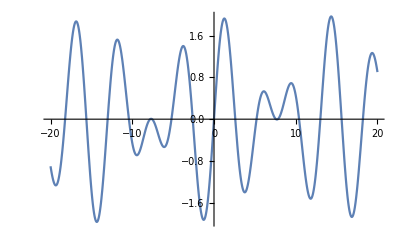

This function plots Sin[Sqrt[2] x]+Sin[x]. This function has  a total of 18 extremas . A proposed description of this plot based on the derivatives and extremas : still a smooth decline that ends at x = -19.3542 then a sharp increase that ends at x = -16.8648 then a sharp decrease that ends at x = -14.3389 then a sharp increase that ends at x = -11.8286 then a smooth decline that ends at x = -9.44122 then a very smooth increase that ends at x = -7.69644 then still a smooth decline that ends at x = -6.09682 then a smooth increase that ends at x = -3.76467 then a sharp decrease that ends at x = -1.26326 then a sharp increase that ends at x = 1.26326 then a sharp decrease that ends at x = 3.76467 then a smooth increase that ends at x = 6.09682 then still a smooth decline that ends at x = 7.69644 then a very smooth increase that ends at x = 9.44122 then a smooth decline that ends at x = 11.8286 then a sharp increase that ends at x = 14.3389 then a sharp decrease that ends at x = 16.8648 then a sharp increase that ends at x = 19.3542 then still a smooth decline that ends at x = 20

```mathematica
f["Sin[Sqrt[2] x]+Sin[x]",-20,20]
```